```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
<<Notation`
```

```mathematica
(* Simplify the notation for the formulas: index vectors based on a subscript notation *)
Notation[Subscript[x_, n_] ⟺ x_[[n_]]]
```

```mathematica
d=1.0; (* Equilibrium bond length *)
α=Reverse@{13.00773,1.962079,0.444529,0.1219492}&/@Range[1,2]//Flatten
```

{0.121949,0.444529,1.96208,13.0077,0.121949,0.444529,1.96208,13.0077}

```mathematica
atomsPts={{0,0,0},{d,0,0}}; (* Atomic positions *)
Z=Partition[Table[#,{n,1,4}]&/@atomsPts//Flatten,3] (* Array of positions for the coefficients α *)
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1.,0,0},{1.,0,0},{1.,0,0},{1.,0,0}}

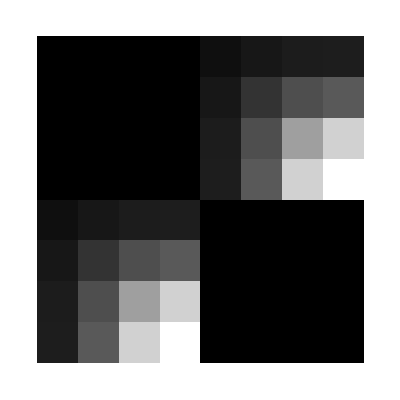
{True,-Graphics-,(1. | 1. | 1. | 1. | 0.940847 | 0.90874 | 0.891533 | 0.886197
1. | 1. | 1. | 1. | 0.90874 | 0.800704 | 0.695991 | 0.650613
1. | 1. | 1. | 1. | 0.891533 | 0.695991 | 0.374921 | 0.181789
1. | 1. | 1. | 1. | 0.886197 | 0.650613 | 0.181789 | 0.00149764
0.940847 | 0.90874 | 0.891533 | 0.886197 | 1. | 1. | 1. | 1.
0.90874 | 0.800704 | 0.695991 | 0.650613 | 1. | 1. | 1. | 1.
0.891533 | 0.695991 | 0.374921 | 0.181789 | 1. | 1. | 1. | 1.
0.886197 | 0.650613 | 0.181789 | 0.00149764 | 1. | 1. | 1. | 1.)}

```mathematica
K=Array[Exp[-(Subscript[α, #1] Subscript[α, #2])/(Subscript[α, #1]+Subscript[α, #2])Norm[Subscript[Z, #1]-Subscript[Z, #2]]^2]&,{8,8}];(* Coefficients matrix Subscript[K, p,q] *)
#[K]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

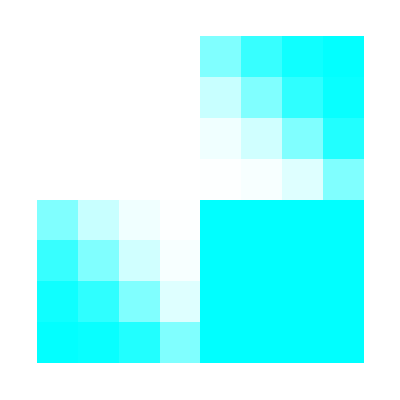
{False,-Graphics-,((0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.5
0.
0.) | (0.784724
0.
0.) | (0.941484
0.
0.) | (0.990712
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.215276
0.
0.) | (0.5
0.
0.) | (0.815288
0.
0.) | (0.966955
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.0585161
0.
0.) | (0.184712
0.
0.) | (0.5
0.
0.) | (0.868931
0.
0.)
(0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.
0.
0.) | (0.00928806
0.
0.) | (0.0330449
0.
0.) | (0.131069
0.
0.) | (0.5
0.
0.)
(0.5
0.
0.) | (0.215276
0.
0.) | (0.0585161
0.
0.) | (0.00928806
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.)
(0.784724
0.
0.) | (0.5
0.
0.) | (0.184712
0.
0.) | (0.0330449
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.)
(0.941484
0.
0.) | (0.815288
0.
0.) | (0.5
0.
0.) | (0.131069
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.)
(0.990712
0.
0.) | (0.966955
0.
0.) | (0.868931
0.
0.) | (0.5
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.) | (1.
0.
0.))}

```mathematica
R=Array[(Subscript[α, #1] Subscript[Z, #1]+Subscript[α, #2] Subscript[Z, #2])/(Subscript[α, #1]+Subscript[α, #2])&,{8,8}];(* Distances matrix Subscript[R, p,q] *)
#[R]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

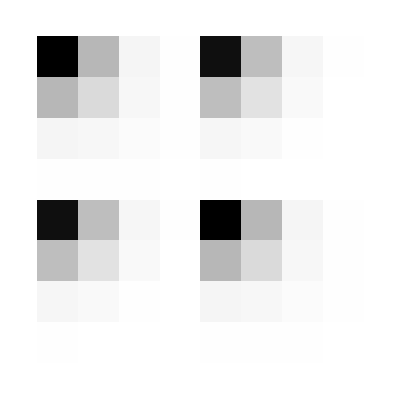
{True,-Graphics-,(46.2287 | 13.0602 | 1.85084 | 0.117043 | 43.4941 | 11.8683 | 1.65009 | 0.103723
13.0602 | 6.64247 | 1.49148 | 0.112858 | 11.8683 | 5.31865 | 1.03805 | 0.0734269
1.85084 | 1.49148 | 0.716317 | 0.0961392 | 1.65009 | 1.03805 | 0.268562 | 0.017477
0.117043 | 0.112858 | 0.0961392 | 0.0419641 | 0.103723 | 0.0734269 | 0.017477 | 0.000062847
43.4941 | 11.8683 | 1.65009 | 0.103723 | 46.2287 | 13.0602 | 1.85084 | 0.117043
11.8683 | 5.31865 | 1.03805 | 0.0734269 | 13.0602 | 6.64247 | 1.49148 | 0.112858
1.65009 | 1.03805 | 0.268562 | 0.017477 | 1.85084 | 1.49148 | 0.716317 | 0.0961392
0.103723 | 0.0734269 | 0.017477 | 0.000062847 | 0.117043 | 0.112858 | 0.0961392 | 0.0419641)}

```mathematica
S=Array[(π/(Subscript[α, #1]+Subscript[α, #2]))^(3/2)Subscript[K, #1,#2]&,{8,8}];(* Overlap matrix Subscript[S, p,q] *)
#[S]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

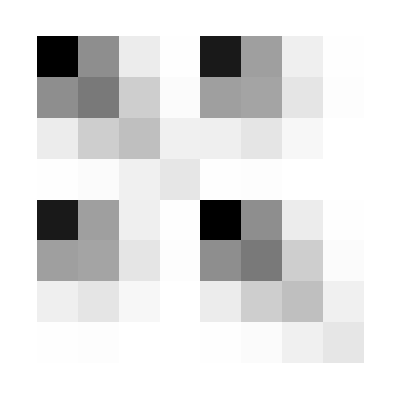
{True,-Graphics-,(8.45632 | 3.74945 | 0.637503 | 0.042422 | 7.63269 | 3.1899 | 0.524852 | 0.0345662
3.74945 | 4.42916 | 1.62162 | 0.145532 | 3.1899 | 3.02094 | 0.85594 | 0.0675523
0.637503 | 1.62162 | 2.1082 | 0.491726 | 0.524852 | 0.85594 | 0.273461 | -0.0122114
0.042422 | 0.145532 | 0.491726 | 0.818786 | 0.0345662 | 0.0675523 | -0.0122114 | -0.00409065
7.63269 | 3.1899 | 0.524852 | 0.0345662 | 8.45632 | 3.74945 | 0.637503 | 0.042422
3.1899 | 3.02094 | 0.85594 | 0.0675523 | 3.74945 | 4.42916 | 1.62162 | 0.145532
0.524852 | 0.85594 | 0.273461 | -0.0122114 | 0.637503 | 1.62162 | 2.1082 | 0.491726
0.0345662 | 0.0675523 | -0.0122114 | -0.00409065 | 0.042422 | 0.145532 | 0.491726 | 0.818786)}

```mathematica
T=Array[(Subscript[α, #1] Subscript[α, #2])/(Subscript[α, #1]+Subscript[α, #2])(3-2(Subscript[α, #1] Subscript[α, #2])/(Subscript[α, #1]+Subscript[α, #2])Norm[Subscript[Z, #1]-Subscript[Z, #2]]^2)Subscript[S, #1,#2]&,{8,8}];(* Kinetic energy matrix Subscript[T, p,q] *)
#[T]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

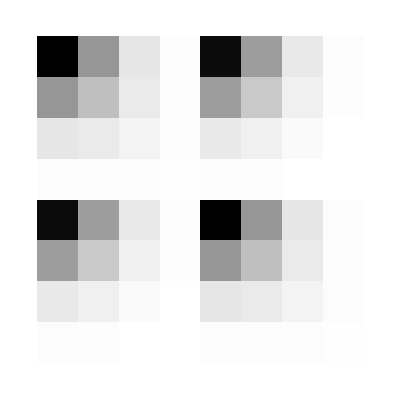
{True,-Graphics-,(-49.5733 | -20.4017 | -4.78952 | -0.595591 | -47.5078 | -19.0125 | -4.33849 | -0.528623
-20.4017 | -12.4983 | -4.06016 | -0.579931 | -19.0125 | -10.5321 | -2.948 | -0.378339
-4.78952 | -4.06016 | -2.31383 | -0.515863 | -4.33849 | -2.948 | -0.900982 | -0.0903486
-0.595591 | -0.579931 | -0.515863 | -0.283481 | -0.528623 | -0.378339 | -0.0903486 | -0.00025131
-47.5078 | -19.0125 | -4.33849 | -0.528623 | -49.5733 | -20.4017 | -4.78952 | -0.595591
-19.0125 | -10.5321 | -2.948 | -0.378339 | -20.4017 | -12.4983 | -4.06016 | -0.579931
-4.33849 | -2.948 | -0.900982 | -0.0903486 | -4.78952 | -4.06016 | -2.31383 | -0.515863
-0.528623 | -0.378339 | -0.0903486 | -0.00025131 | -0.595591 | -0.579931 | -0.515863 | -0.283481)}

```mathematica
V=Total@Table[Array[If[Norm[Subscript[R, #1,#2]-U]==0,-(2π)/(Subscript[α, #1]+Subscript[α, #2])Subscript[K, #1,#2],-Subscript[S, #1,#2] 1/Norm[Subscript[R, #1,#2]-U] Erf[√(Subscript[α, #1]+Subscript[α, #2])Norm[Subscript[R, #1,#2]-U]]]&,{8,8}],{U,atomsPts}];(* Potential energy matrix Subscript[V, p,q] *)
#[V]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

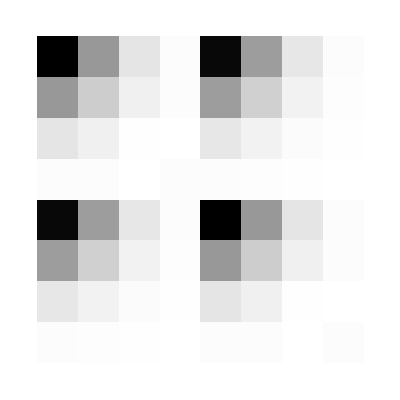
{True,-Graphics-,(-41.117 | -16.6522 | -4.15202 | -0.553169 | -39.8751 | -15.8226 | -3.81364 | -0.494057
-16.6522 | -8.06909 | -2.43854 | -0.434398 | -15.8226 | -7.51116 | -2.09206 | -0.310786
-4.15202 | -2.43854 | -0.205623 | -0.0241367 | -3.81364 | -2.09206 | -0.627521 | -0.10256
-0.553169 | -0.434398 | -0.0241367 | 0.535304 | -0.494057 | -0.310786 | -0.10256 | -0.00434196
-39.8751 | -15.8226 | -3.81364 | -0.494057 | -41.117 | -16.6522 | -4.15202 | -0.553169
-15.8226 | -7.51116 | -2.09206 | -0.310786 | -16.6522 | -8.06909 | -2.43854 | -0.434398
-3.81364 | -2.09206 | -0.627521 | -0.10256 | -4.15202 | -2.43854 | -0.205623 | -0.0241367
-0.494057 | -0.310786 | -0.10256 | -0.00434196 | -0.553169 | -0.434398 | -0.0241367 | 0.535304)}

```mathematica
H=T+V;
#[H]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

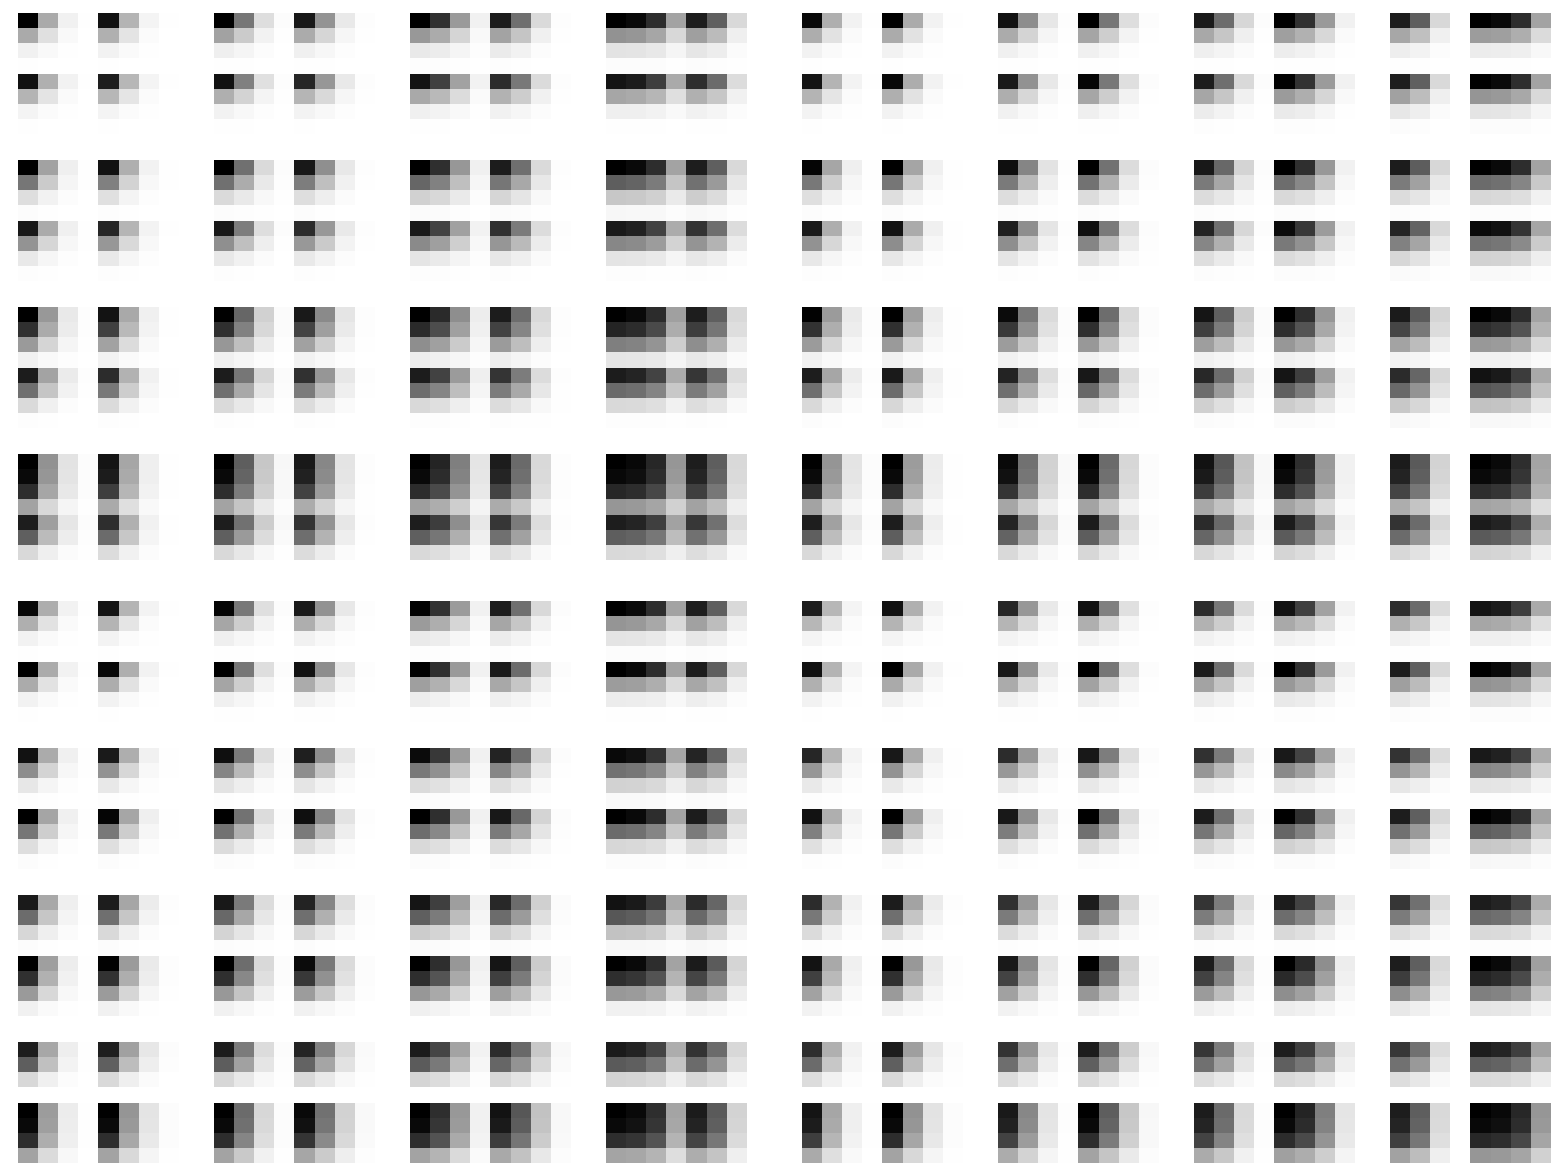
{False,-Graphics-,((842.107 | 281.3 | 45.1136 | 2.98757 | 784.315 | 246.957 | 37.7695 | 2.454
281.3 | 102.431 | 18.2034 | 1.27107 | 260.947 | 87.9432 | 14.3241 | 0.954612
45.1136 | 18.2034 | 3.94576 | 0.327815 | 41.6852 | 15.1465 | 2.67911 | 0.1821
2.98757 | 1.27107 | 0.327815 | 0.0396054 | 2.75575 | 1.03827 | 0.189921 | 0.0122497
784.315 | 260.947 | 41.6852 | 2.75575 | 745.428 | 239.404 | 37.3111 | 2.4439
246.957 | 87.9432 | 15.1465 | 1.03827 | 239.404 | 84.5884 | 14.6943 | 1.01581
37.7695 | 14.3241 | 2.67911 | 0.189921 | 37.3111 | 14.6943 | 3.13621 | 0.258622
2.454 | 0.954612 | 0.1821 | 0.0122497 | 2.4439 | 1.01581 | 0.258622 | 0.0311039) | (281.3 | 151.586 | 36.6122 | 2.88138 | 254.956 | 119.467 | 24.2848 | 1.74363
102.431 | 57.5811 | 14.8838 | 1.22623 | 92.6775 | 44.8098 | 9.39615 | 0.680982
18.2034 | 10.9513 | 3.29186 | 0.316616 | 16.4291 | 8.3339 | 1.83097 | 0.131239
1.27107 | 0.800509 | 0.280913 | 0.0384204 | 1.14545 | 0.599139 | 0.134104 | 0.008884
260.947 | 140.377 | 33.8212 | 2.65778 | 239.404 | 114.196 | 23.7997 | 1.73354
87.9432 | 48.8358 | 12.3534 | 1.00154 | 82.0685 | 41.5093 | 9.41225 | 0.720655
14.3241 | 8.2283 | 2.19737 | 0.183225 | 13.6702 | 7.51233 | 2.03055 | 0.183579
0.954612 | 0.5556 | 0.149014 | 0.0118121 | 0.922318 | 0.53224 | 0.169715 | 0.0221245) | (45.1136 | 36.6122 | 17.9053 | 2.45676 | 40.2102 | 25.4177 | 6.58681 | 0.42104
18.2034 | 14.8838 | 7.42713 | 1.04672 | 16.2207 | 10.3052 | 2.67386 | 0.167081
3.94576 | 3.29186 | 1.74535 | 0.271565 | 3.51359 | 2.26233 | 0.587146 | 0.0336341
0.327815 | 0.280913 | 0.164435 | 0.0335803 | 0.291659 | 0.191083 | 0.0490956 | 0.00235139
41.6852 | 33.8212 | 16.5293 | 2.26603 | 37.3111 | 23.7997 | 6.31599 | 0.415661
15.1465 | 12.3534 | 6.12195 | 0.854567 | 13.6702 | 8.92026 | 2.49702 | 0.172694
2.67911 | 2.19737 | 1.10438 | 0.156412 | 2.45945 | 1.67936 | 0.53566 | 0.0438718
0.1821 | 0.149014 | 0.0738789 | 0.0100632 | 0.169452 | 0.119687 | 0.0438392 | 0.00522842) | (2.98757 | 2.88138 | 2.45676 | 1.07602 | 2.64755 | 1.8745 | 0.445997 | 0.00157963
1.27107 | 1.22623 | 1.04672 | 0.460465 | 1.1264 | 0.797644 | 0.189689 | 0.000659032
0.327815 | 0.316616 | 0.271565 | 0.121736 | 0.290494 | 0.205859 | 0.0488551 | 0.0001568
0.0396054 | 0.0384204 | 0.0335803 | 0.0163712 | 0.0350915 | 0.0249365 | 0.00586858 | 0.0000141712
2.75575 | 2.65778 | 2.26603 | 0.992353 | 2.4439 | 1.73354 | 0.415661 | 0.00151617
1.03827 | 1.00154 | 0.854567 | 0.37533 | 0.922318 | 0.657137 | 0.160365 | 0.000617413
0.189921 | 0.183225 | 0.156412 | 0.0688123 | 0.169452 | 0.122118 | 0.0312753 | 0.000144273
0.0122497 | 0.0118121 | 0.0100632 | 0.00439328 | 0.0109579 | 0.00794887 | 0.00210599 | 0.0000127478) | (784.315 | 254.956 | 40.2102 | 2.64755 | 809.092 | 266.099 | 42.0345 | 2.76531
260.947 | 92.6775 | 16.2207 | 1.1264 | 266.099 | 93.5295 | 15.8267 | 1.07409
41.6852 | 16.4291 | 3.51359 | 0.290494 | 42.0345 | 15.8267 | 2.91572 | 0.204089
2.75575 | 1.14545 | 0.291659 | 0.0350915 | 2.76531 | 1.07409 | 0.204089 | 0.013695
745.428 | 239.404 | 37.3111 | 2.4439 | 784.315 | 260.947 | 41.6852 | 2.75575
239.404 | 82.0685 | 13.6702 | 0.922318 | 254.956 | 92.6775 | 16.4291 | 1.14545
37.3111 | 13.6702 | 2.45945 | 0.169452 | 40.2102 | 16.2207 | 3.51359 | 0.291659
2.4439 | 0.922318 | 0.169452 | 0.0109579 | 2.64755 | 1.1264 | 0.290494 | 0.0350915) | (246.957 | 119.467 | 25.4177 | 1.8745 | 266.099 | 142.446 | 34.08 | 2.66694
87.9432 | 44.8098 | 10.3052 | 0.797644 | 93.5295 | 51.5761 | 12.8904 | 1.03604
15.1465 | 8.3339 | 2.26233 | 0.205859 | 15.8267 | 9.04553 | 2.38775 | 0.196878
1.03827 | 0.599139 | 0.191083 | 0.0249365 | 1.07409 | 0.624385 | 0.166936 | 0.0132056
239.404 | 114.196 | 23.7997 | 1.73354 | 260.947 | 140.377 | 33.8212 | 2.65778
84.5884 | 41.5093 | 8.92026 | 0.657137 | 92.6775 | 52.0479 | 13.4303 | 1.10504
14.6943 | 7.51233 | 1.67936 | 0.122118 | 16.2207 | 9.75654 | 2.93107 | 0.281693
1.01581 | 0.53224 | 0.119687 | 0.00794887 | 1.1264 | 0.709391 | 0.248929 | 0.0340415) | (37.7695 | 24.2848 | 6.58681 | 0.445997 | 42.0345 | 34.08 | 16.6243 | 2.2736
14.3241 | 9.39615 | 2.67386 | 0.189689 | 15.8267 | 12.8904 | 6.36406 | 0.883807
2.67911 | 1.83097 | 0.587146 | 0.0488551 | 2.91572 | 2.38775 | 1.1946 | 0.168014
0.189921 | 0.134104 | 0.0490956 | 0.00586858 | 0.204089 | 0.166936 | 0.0826686 | 0.0112503
37.3111 | 23.7997 | 6.31599 | 0.415661 | 41.6852 | 33.8212 | 16.5293 | 2.26603
14.6943 | 9.41225 | 2.49702 | 0.160365 | 16.4291 | 13.4303 | 6.69807 | 0.943239
3.13621 | 2.03055 | 0.53566 | 0.0312753 | 3.51359 | 2.93107 | 1.55362 | 0.241604
0.258622 | 0.169715 | 0.0438392 | 0.00210599 | 0.290494 | 0.248929 | 0.145709 | 0.0297528) | (2.454 | 1.74363 | 0.42104 | 0.00157963 | 2.76531 | 2.66694 | 2.2736 | 0.995294
0.954612 | 0.680982 | 0.167081 | 0.000659032 | 1.07409 | 1.03604 | 0.883807 | 0.38784
0.1821 | 0.131239 | 0.0336341 | 0.0001568 | 0.204089 | 0.196878 | 0.168014 | 0.0738257
0.0122497 | 0.008884 | 0.00235139 | 0.0000141712 | 0.013695 | 0.0132056 | 0.0112503 | 0.00491143
2.4439 | 1.73354 | 0.415661 | 0.00151617 | 2.75575 | 2.65778 | 2.26603 | 0.992353
1.01581 | 0.720655 | 0.172694 | 0.000617413 | 1.14545 | 1.10504 | 0.943239 | 0.414887
0.258622 | 0.183579 | 0.0438718 | 0.000144273 | 0.291659 | 0.281693 | 0.241604 | 0.108293
0.0311039 | 0.0221245 | 0.00522842 | 0.0000127478 | 0.0350915 | 0.0340415 | 0.0297528 | 0.0145044)
(281.3 | 102.431 | 18.2034 | 1.27107 | 260.947 | 87.9432 | 14.3241 | 0.954612
151.586 | 57.5811 | 10.9513 | 0.800509 | 140.377 | 48.8358 | 8.2283 | 0.5556
36.6122 | 14.8838 | 3.29186 | 0.280913 | 33.8212 | 12.3534 | 2.19737 | 0.149014
2.88138 | 1.22623 | 0.316616 | 0.0384204 | 2.65778 | 1.00154 | 0.183225 | 0.0118121
254.956 | 92.6775 | 16.4291 | 1.14545 | 239.404 | 82.0685 | 13.6702 | 0.922318
119.467 | 44.8098 | 8.3339 | 0.599139 | 114.196 | 41.5093 | 7.51233 | 0.53224
24.2848 | 9.39615 | 1.83097 | 0.134104 | 23.7997 | 9.41225 | 2.03055 | 0.169715
1.74363 | 0.680982 | 0.131239 | 0.008884 | 1.73354 | 0.720655 | 0.183579 | 0.0221245) | (102.431 | 57.5811 | 14.8838 | 1.22623 | 92.6775 | 44.8098 | 9.39615 | 0.680982
57.5811 | 33.1944 | 9.00736 | 0.772476 | 52.0479 | 25.6262 | 5.47296 | 0.3976
14.8838 | 9.00736 | 2.75344 | 0.271374 | 13.4303 | 6.84032 | 1.5079 | 0.107512
1.22623 | 0.772476 | 0.271374 | 0.0372736 | 1.10504 | 0.5781 | 0.1294 | 0.00856665
92.6775 | 52.0479 | 13.4303 | 1.10504 | 84.5884 | 41.5093 | 8.92026 | 0.657137
44.8098 | 25.6262 | 6.84032 | 0.5781 | 41.5093 | 21.2818 | 4.91372 | 0.379303
9.39615 | 5.47296 | 1.5079 | 0.1294 | 8.92026 | 4.91372 | 1.33378 | 0.120987
0.680982 | 0.3976 | 0.107512 | 0.00856665 | 0.657137 | 0.379303 | 0.120987 | 0.0157778) | (18.2034 | 14.8838 | 7.42713 | 1.04672 | 16.2207 | 10.3052 | 2.67386 | 0.167081
10.9513 | 9.00736 | 4.57099 | 0.660119 | 9.75654 | 6.22306 | 1.61564 | 0.0988282
3.29186 | 2.75344 | 1.4724 | 0.232972 | 2.93107 | 1.89047 | 0.490451 | 0.0276938
0.316616 | 0.271374 | 0.158995 | 0.0325886 | 0.281693 | 0.184579 | 0.0474176 | 0.0022675
16.4291 | 13.4303 | 6.69807 | 0.943239 | 14.6943 | 9.41225 | 2.49702 | 0.160365
8.3339 | 6.84032 | 3.45045 | 0.49381 | 7.51233 | 4.91372 | 1.37221 | 0.0925496
1.83097 | 1.5079 | 0.766969 | 0.110549 | 1.67936 | 1.14841 | 0.366034 | 0.0294178
0.131239 | 0.107512 | 0.0534615 | 0.00729845 | 0.122118 | 0.0863339 | 0.0316843 | 0.00376867) | (1.27107 | 1.22623 | 1.04672 | 0.460465 | 1.1264 | 0.797644 | 0.189689 | 0.000659032
0.800509 | 0.772476 | 0.660119 | 0.291629 | 0.709391 | 0.502431 | 0.119428 | 0.000407384
0.280913 | 0.271374 | 0.232972 | 0.104819 | 0.248929 | 0.176428 | 0.0418541 | 0.000132362
0.0384204 | 0.0372736 | 0.0325886 | 0.0159132 | 0.0340415 | 0.0241915 | 0.0056924 | 0.0000136857
1.14545 | 1.10504 | 0.943239 | 0.414887 | 1.01581 | 0.720655 | 0.172694 | 0.000617413
0.599139 | 0.5781 | 0.49381 | 0.217805 | 0.53224 | 0.379303 | 0.0925496 | 0.000349711
0.134104 | 0.1294 | 0.110549 | 0.04878 | 0.119687 | 0.0863339 | 0.0221789 | 0.00010178
0.008884 | 0.00856665 | 0.00729845 | 0.00318644 | 0.00794887 | 0.0057695 | 0.0015327 | 9.39577×10^-6) | (260.947 | 92.6775 | 16.2207 | 1.1264 | 266.099 | 93.5295 | 15.8267 | 1.07409
140.377 | 52.0479 | 9.75654 | 0.709391 | 142.446 | 51.5761 | 9.04553 | 0.624385
33.8212 | 13.4303 | 2.93107 | 0.248929 | 34.08 | 12.8904 | 2.38775 | 0.166936
2.65778 | 1.10504 | 0.281693 | 0.0340415 | 2.66694 | 1.03604 | 0.196878 | 0.0132056
239.404 | 84.5884 | 14.6943 | 1.01581 | 246.957 | 87.9432 | 15.1465 | 1.03827
114.196 | 41.5093 | 7.51233 | 0.53224 | 119.467 | 44.8098 | 8.3339 | 0.599139
23.7997 | 8.92026 | 1.67936 | 0.119687 | 25.4177 | 10.3052 | 2.26233 | 0.191083
1.73354 | 0.657137 | 0.122118 | 0.00794887 | 1.8745 | 0.797644 | 0.205859 | 0.0249365) | (87.9432 | 44.8098 | 10.3052 | 0.797644 | 93.5295 | 51.5761 | 12.8904 | 1.03604
48.8358 | 25.6262 | 6.22306 | 0.502431 | 51.5761 | 28.8679 | 7.38576 | 0.602317
12.3534 | 6.84032 | 1.89047 | 0.176428 | 12.8904 | 7.38576 | 1.95573 | 0.161033
1.00154 | 0.5781 | 0.184579 | 0.0241915 | 1.03604 | 0.602317 | 0.161033 | 0.0127338
82.0685 | 41.5093 | 9.41225 | 0.720655 | 87.9432 | 48.8358 | 12.3534 | 1.00154
41.5093 | 21.2818 | 4.91372 | 0.379303 | 44.8098 | 25.6262 | 6.84032 | 0.5781
9.41225 | 4.91372 | 1.14841 | 0.0863339 | 10.3052 | 6.22306 | 1.89047 | 0.184579
0.720655 | 0.379303 | 0.0863339 | 0.0057695 | 0.797644 | 0.502431 | 0.176428 | 0.0241915) | (14.3241 | 9.39615 | 2.67386 | 0.189689 | 15.8267 | 12.8904 | 6.36406 | 0.883807
8.2283 | 5.47296 | 1.61564 | 0.119428 | 9.04553 | 7.38576 | 3.6705 | 0.51399
2.19737 | 1.5079 | 0.490451 | 0.0418541 | 2.38775 | 1.95573 | 0.978502 | 0.137407
0.183225 | 0.1294 | 0.0474176 | 0.0056924 | 0.196878 | 0.161033 | 0.0797342 | 0.0108483
13.6702 | 8.92026 | 2.49702 | 0.172694 | 15.1465 | 12.3534 | 6.12195 | 0.854567
7.51233 | 4.91372 | 1.37221 | 0.0925496 | 8.3339 | 6.84032 | 3.45045 | 0.49381
2.03055 | 1.33378 | 0.366034 | 0.0221789 | 2.26233 | 1.89047 | 1.00765 | 0.158403
0.183579 | 0.120987 | 0.0316843 | 0.0015327 | 0.205859 | 0.176428 | 0.10333 | 0.021148) | (0.954612 | 0.680982 | 0.167081 | 0.000659032 | 1.07409 | 1.03604 | 0.883807 | 0.38784
0.5556 | 0.3976 | 0.0988282 | 0.000407384 | 0.624385 | 0.602317 | 0.51399 | 0.225846
0.149014 | 0.107512 | 0.0276938 | 0.000132362 | 0.166936 | 0.161033 | 0.137407 | 0.0603466
0.0118121 | 0.00856665 | 0.0022675 | 0.0000136857 | 0.0132056 | 0.0127338 | 0.0108483 | 0.00473586
0.922318 | 0.657137 | 0.160365 | 0.000617413 | 1.03827 | 1.00154 | 0.854567 | 0.37533
0.53224 | 0.379303 | 0.0925496 | 0.000349711 | 0.599139 | 0.5781 | 0.49381 | 0.217805
0.169715 | 0.120987 | 0.0294178 | 0.00010178 | 0.191083 | 0.184579 | 0.158403 | 0.0711659
0.0221245 | 0.0157778 | 0.00376867 | 9.39577×10^-6 | 0.0249365 | 0.0241915 | 0.021148 | 0.01032)
(45.1136 | 18.2034 | 3.94576 | 0.327815 | 41.6852 | 15.1465 | 2.67911 | 0.1821
36.6122 | 14.8838 | 3.29186 | 0.280913 | 33.8212 | 12.3534 | 2.19737 | 0.149014
17.9053 | 7.42713 | 1.74535 | 0.164435 | 16.5293 | 6.12195 | 1.10438 | 0.0738789
2.45676 | 1.04672 | 0.271565 | 0.0335803 | 2.26603 | 0.854567 | 0.156412 | 0.0100632
40.2102 | 16.2207 | 3.51359 | 0.291659 | 37.3111 | 13.6702 | 2.45945 | 0.169452
25.4177 | 10.3052 | 2.26233 | 0.191083 | 23.7997 | 8.92026 | 1.67936 | 0.119687
6.58681 | 2.67386 | 0.587146 | 0.0490956 | 6.31599 | 2.49702 | 0.53566 | 0.0438392
0.42104 | 0.167081 | 0.0336341 | 0.00235139 | 0.415661 | 0.172694 | 0.0438718 | 0.00522842) | (18.2034 | 10.9513 | 3.29186 | 0.316616 | 16.4291 | 8.3339 | 1.83097 | 0.131239
14.8838 | 9.00736 | 2.75344 | 0.271374 | 13.4303 | 6.84032 | 1.5079 | 0.107512
7.42713 | 4.57099 | 1.4724 | 0.158995 | 6.69807 | 3.45045 | 0.766969 | 0.0534615
1.04672 | 0.660119 | 0.232972 | 0.0325886 | 0.943239 | 0.49381 | 0.110549 | 0.00729845
16.2207 | 9.75654 | 2.93107 | 0.281693 | 14.6943 | 7.51233 | 1.67936 | 0.122118
10.3052 | 6.22306 | 1.89047 | 0.184579 | 9.41225 | 4.91372 | 1.14841 | 0.0863339
2.67386 | 1.61564 | 0.490451 | 0.0474176 | 2.49702 | 1.37221 | 0.366034 | 0.0316843
0.167081 | 0.0988282 | 0.0276938 | 0.0022675 | 0.160365 | 0.0925496 | 0.0294178 | 0.00376867) | (3.94576 | 3.29186 | 1.74535 | 0.271565 | 3.51359 | 2.26233 | 0.587146 | 0.0336341
3.29186 | 2.75344 | 1.4724 | 0.232972 | 2.93107 | 1.89047 | 0.490451 | 0.0276938
1.74535 | 1.4724 | 0.811005 | 0.137019 | 1.55362 | 1.00765 | 0.260884 | 0.0139716
0.271565 | 0.232972 | 0.137019 | 0.0285331 | 0.241604 | 0.158403 | 0.0406674 | 0.00193217
3.51359 | 2.93107 | 1.55362 | 0.241604 | 3.13621 | 2.03055 | 0.53566 | 0.0312753
2.26233 | 1.89047 | 1.00765 | 0.158403 | 2.03055 | 1.33378 | 0.366034 | 0.0221789
0.587146 | 0.490451 | 0.260884 | 0.0406674 | 0.53566 | 0.366034 | 0.114 | 0.00817306
0.0336341 | 0.0276938 | 0.0139716 | 0.00193217 | 0.0312753 | 0.0221789 | 0.00817306 | 0.000942936) | (0.327815 | 0.316616 | 0.271565 | 0.121736 | 0.290494 | 0.205859 | 0.0488551 | 0.0001568
0.280913 | 0.271374 | 0.232972 | 0.104819 | 0.248929 | 0.176428 | 0.0418541 | 0.000132362
0.164435 | 0.158995 | 0.137019 | 0.062633 | 0.145709 | 0.10333 | 0.024472 | 0.0000727815
0.0335803 | 0.0325886 | 0.0285331 | 0.0140328 | 0.0297528 | 0.021148 | 0.00497299 | 0.0000117303
0.291659 | 0.281693 | 0.241604 | 0.108293 | 0.258622 | 0.183579 | 0.0438718 | 0.000144273
0.191083 | 0.184579 | 0.158403 | 0.0711659 | 0.169715 | 0.120987 | 0.0294178 | 0.00010178
0.0490956 | 0.0474176 | 0.0406674 | 0.0182202 | 0.0438392 | 0.0316843 | 0.00817306 | 0.0000351683
0.00235139 | 0.0022675 | 0.00193217 | 0.000843904 | 0.00210599 | 0.0015327 | 0.000412178 | 2.65635×10^-6) | (41.6852 | 16.4291 | 3.51359 | 0.290494 | 42.0345 | 15.8267 | 2.91572 | 0.204089
33.8212 | 13.4303 | 2.93107 | 0.248929 | 34.08 | 12.8904 | 2.38775 | 0.166936
16.5293 | 6.69807 | 1.55362 | 0.145709 | 16.6243 | 6.36406 | 1.1946 | 0.0826686
2.26603 | 0.943239 | 0.241604 | 0.0297528 | 2.2736 | 0.883807 | 0.168014 | 0.0112503
37.3111 | 14.6943 | 3.13621 | 0.258622 | 37.7695 | 14.3241 | 2.67911 | 0.189921
23.7997 | 9.41225 | 2.03055 | 0.169715 | 24.2848 | 9.39615 | 1.83097 | 0.134104
6.31599 | 2.49702 | 0.53566 | 0.0438392 | 6.58681 | 2.67386 | 0.587146 | 0.0490956
0.415661 | 0.160365 | 0.0312753 | 0.00210599 | 0.445997 | 0.189689 | 0.0488551 | 0.00586858) | (15.1465 | 8.3339 | 2.26233 | 0.205859 | 15.8267 | 9.04553 | 2.38775 | 0.196878
12.3534 | 6.84032 | 1.89047 | 0.176428 | 12.8904 | 7.38576 | 1.95573 | 0.161033
6.12195 | 3.45045 | 1.00765 | 0.10333 | 6.36406 | 3.6705 | 0.978502 | 0.0797342
0.854567 | 0.49381 | 0.158403 | 0.021148 | 0.883807 | 0.51399 | 0.137407 | 0.0108483
13.6702 | 7.51233 | 2.03055 | 0.183579 | 14.3241 | 8.2283 | 2.19737 | 0.183225
8.92026 | 4.91372 | 1.33378 | 0.120987 | 9.39615 | 5.47296 | 1.5079 | 0.1294
2.49702 | 1.37221 | 0.366034 | 0.0316843 | 2.67386 | 1.61564 | 0.490451 | 0.0474176
0.172694 | 0.0925496 | 0.0221789 | 0.0015327 | 0.189689 | 0.119428 | 0.0418541 | 0.0056924) | (2.67911 | 1.83097 | 0.587146 | 0.0488551 | 2.91572 | 2.38775 | 1.1946 | 0.168014
2.19737 | 1.5079 | 0.490451 | 0.0418541 | 2.38775 | 1.95573 | 0.978502 | 0.137407
1.10438 | 0.766969 | 0.260884 | 0.024472 | 1.1946 | 0.978502 | 0.488687 | 0.0679954
0.156412 | 0.110549 | 0.0406674 | 0.00497299 | 0.168014 | 0.137407 | 0.0679954 | 0.00924173
2.45945 | 1.67936 | 0.53566 | 0.0438718 | 2.67911 | 2.19737 | 1.10438 | 0.156412
1.67936 | 1.14841 | 0.366034 | 0.0294178 | 1.83097 | 1.5079 | 0.766969 | 0.110549
0.53566 | 0.366034 | 0.114 | 0.00817306 | 0.587146 | 0.490451 | 0.260884 | 0.0406674
0.0438718 | 0.0294178 | 0.00817306 | 0.000412178 | 0.0488551 | 0.0418541 | 0.024472 | 0.00497299) | (0.1821 | 0.131239 | 0.0336341 | 0.0001568 | 0.204089 | 0.196878 | 0.168014 | 0.0738257
0.149014 | 0.107512 | 0.0276938 | 0.000132362 | 0.166936 | 0.161033 | 0.137407 | 0.0603466
0.0738789 | 0.0534615 | 0.0139716 | 0.0000727815 | 0.0826686 | 0.0797342 | 0.0679954 | 0.0297885
0.0100632 | 0.00729845 | 0.00193217 | 0.0000117303 | 0.0112503 | 0.0108483 | 0.00924173 | 0.00403434
0.169452 | 0.122118 | 0.0312753 | 0.000144273 | 0.189921 | 0.183225 | 0.156412 | 0.0688123
0.119687 | 0.0863339 | 0.0221789 | 0.00010178 | 0.134104 | 0.1294 | 0.110549 | 0.04878
0.0438392 | 0.0316843 | 0.00817306 | 0.0000351683 | 0.0490956 | 0.0474176 | 0.0406674 | 0.0182202
0.00522842 | 0.00376867 | 0.000942936 | 2.65635×10^-6 | 0.00586858 | 0.0056924 | 0.00497299 | 0.00241873)
(2.98757 | 1.27107 | 0.327815 | 0.0396054 | 2.75575 | 1.03827 | 0.189921 | 0.0122497
2.88138 | 1.22623 | 0.316616 | 0.0384204 | 2.65778 | 1.00154 | 0.183225 | 0.0118121
2.45676 | 1.04672 | 0.271565 | 0.0335803 | 2.26603 | 0.854567 | 0.156412 | 0.0100632
1.07602 | 0.460465 | 0.121736 | 0.0163712 | 0.992353 | 0.37533 | 0.0688123 | 0.00439328
2.64755 | 1.1264 | 0.290494 | 0.0350915 | 2.4439 | 0.922318 | 0.169452 | 0.0109579
1.8745 | 0.797644 | 0.205859 | 0.0249365 | 1.73354 | 0.657137 | 0.122118 | 0.00794887
0.445997 | 0.189689 | 0.0488551 | 0.00586858 | 0.415661 | 0.160365 | 0.0312753 | 0.00210599
0.00157963 | 0.000659032 | 0.0001568 | 0.0000141712 | 0.00151617 | 0.000617413 | 0.000144273 | 0.0000127478) | (1.27107 | 0.800509 | 0.280913 | 0.0384204 | 1.14545 | 0.599139 | 0.134104 | 0.008884
1.22623 | 0.772476 | 0.271374 | 0.0372736 | 1.10504 | 0.5781 | 0.1294 | 0.00856665
1.04672 | 0.660119 | 0.232972 | 0.0325886 | 0.943239 | 0.49381 | 0.110549 | 0.00729845
0.460465 | 0.291629 | 0.104819 | 0.0159132 | 0.414887 | 0.217805 | 0.04878 | 0.00318644
1.1264 | 0.709391 | 0.248929 | 0.0340415 | 1.01581 | 0.53224 | 0.119687 | 0.00794887
0.797644 | 0.502431 | 0.176428 | 0.0241915 | 0.720655 | 0.379303 | 0.0863339 | 0.0057695
0.189689 | 0.119428 | 0.0418541 | 0.0056924 | 0.172694 | 0.0925496 | 0.0221789 | 0.0015327
0.000659032 | 0.000407384 | 0.000132362 | 0.0000136857 | 0.000617413 | 0.000349711 | 0.00010178 | 9.39577×10^-6) | (0.327815 | 0.280913 | 0.164435 | 0.0335803 | 0.291659 | 0.191083 | 0.0490956 | 0.00235139
0.316616 | 0.271374 | 0.158995 | 0.0325886 | 0.281693 | 0.184579 | 0.0474176 | 0.0022675
0.271565 | 0.232972 | 0.137019 | 0.0285331 | 0.241604 | 0.158403 | 0.0406674 | 0.00193217
0.121736 | 0.104819 | 0.062633 | 0.0140328 | 0.108293 | 0.0711659 | 0.0182202 | 0.000843904
0.290494 | 0.248929 | 0.145709 | 0.0297528 | 0.258622 | 0.169715 | 0.0438392 | 0.00210599
0.205859 | 0.176428 | 0.10333 | 0.021148 | 0.183579 | 0.120987 | 0.0316843 | 0.0015327
0.0488551 | 0.0418541 | 0.024472 | 0.00497299 | 0.0438718 | 0.0294178 | 0.00817306 | 0.000412178
0.0001568 | 0.000132362 | 0.0000727815 | 0.0000117303 | 0.000144273 | 0.00010178 | 0.0000351683 | 2.65635×10^-6) | (0.0396054 | 0.0384204 | 0.0335803 | 0.0163712 | 0.0350915 | 0.0249365 | 0.00586858 | 0.0000141712
0.0384204 | 0.0372736 | 0.0325886 | 0.0159132 | 0.0340415 | 0.0241915 | 0.0056924 | 0.0000136857
0.0335803 | 0.0325886 | 0.0285331 | 0.0140328 | 0.0297528 | 0.021148 | 0.00497299 | 0.0000117303
0.0163712 | 0.0159132 | 0.0140328 | 0.00716656 | 0.0145044 | 0.01032 | 0.00241873 | 5.21786×10^-6
0.0350915 | 0.0340415 | 0.0297528 | 0.0145044 | 0.0311039 | 0.0221245 | 0.00522842 | 0.0000127478
0.0249365 | 0.0241915 | 0.021148 | 0.01032 | 0.0221245 | 0.0157778 | 0.00376867 | 9.39577×10^-6
0.00586858 | 0.0056924 | 0.00497299 | 0.00241873 | 0.00522842 | 0.00376867 | 0.000942936 | 2.65635×10^-6
0.0000141712 | 0.0000136857 | 0.0000117303 | 5.21786×10^-6 | 0.0000127478 | 9.39577×10^-6 | 2.65635×10^-6 | 1.60741×10^-8) | (2.75575 | 1.14545 | 0.291659 | 0.0350915 | 2.76531 | 1.07409 | 0.204089 | 0.013695
2.65778 | 1.10504 | 0.281693 | 0.0340415 | 2.66694 | 1.03604 | 0.196878 | 0.0132056
2.26603 | 0.943239 | 0.241604 | 0.0297528 | 2.2736 | 0.883807 | 0.168014 | 0.0112503
0.992353 | 0.414887 | 0.108293 | 0.0145044 | 0.995294 | 0.38784 | 0.0738257 | 0.00491143
2.4439 | 1.01581 | 0.258622 | 0.0311039 | 2.454 | 0.954612 | 0.1821 | 0.0122497
1.73354 | 0.720655 | 0.183579 | 0.0221245 | 1.74363 | 0.680982 | 0.131239 | 0.008884
0.415661 | 0.172694 | 0.0438718 | 0.00522842 | 0.42104 | 0.167081 | 0.0336341 | 0.00235139
0.00151617 | 0.000617413 | 0.000144273 | 0.0000127478 | 0.00157963 | 0.000659032 | 0.0001568 | 0.0000141712) | (1.03827 | 0.599139 | 0.191083 | 0.0249365 | 1.07409 | 0.624385 | 0.166936 | 0.0132056
1.00154 | 0.5781 | 0.184579 | 0.0241915 | 1.03604 | 0.602317 | 0.161033 | 0.0127338
0.854567 | 0.49381 | 0.158403 | 0.021148 | 0.883807 | 0.51399 | 0.137407 | 0.0108483
0.37533 | 0.217805 | 0.0711659 | 0.01032 | 0.38784 | 0.225846 | 0.0603466 | 0.00473586
0.922318 | 0.53224 | 0.169715 | 0.0221245 | 0.954612 | 0.5556 | 0.149014 | 0.0118121
0.657137 | 0.379303 | 0.120987 | 0.0157778 | 0.680982 | 0.3976 | 0.107512 | 0.00856665
0.160365 | 0.0925496 | 0.0294178 | 0.00376867 | 0.167081 | 0.0988282 | 0.0276938 | 0.0022675
0.000617413 | 0.000349711 | 0.00010178 | 9.39577×10^-6 | 0.000659032 | 0.000407384 | 0.000132362 | 0.0000136857) | (0.189921 | 0.134104 | 0.0490956 | 0.00586858 | 0.204089 | 0.166936 | 0.0826686 | 0.0112503
0.183225 | 0.1294 | 0.0474176 | 0.0056924 | 0.196878 | 0.161033 | 0.0797342 | 0.0108483
0.156412 | 0.110549 | 0.0406674 | 0.00497299 | 0.168014 | 0.137407 | 0.0679954 | 0.00924173
0.0688123 | 0.04878 | 0.0182202 | 0.00241873 | 0.0738257 | 0.0603466 | 0.0297885 | 0.00403434
0.169452 | 0.119687 | 0.0438392 | 0.00522842 | 0.1821 | 0.149014 | 0.0738789 | 0.0100632
0.122118 | 0.0863339 | 0.0316843 | 0.00376867 | 0.131239 | 0.107512 | 0.0534615 | 0.00729845
0.0312753 | 0.0221789 | 0.00817306 | 0.000942936 | 0.0336341 | 0.0276938 | 0.0139716 | 0.00193217
0.000144273 | 0.00010178 | 0.0000351683 | 2.65635×10^-6 | 0.0001568 | 0.000132362 | 0.0000727815 | 0.0000117303) | (0.0122497 | 0.008884 | 0.00235139 | 0.0000141712 | 0.013695 | 0.0132056 | 0.0112503 | 0.00491143
0.0118121 | 0.00856665 | 0.0022675 | 0.0000136857 | 0.0132056 | 0.0127338 | 0.0108483 | 0.00473586
0.0100632 | 0.00729845 | 0.00193217 | 0.0000117303 | 0.0112503 | 0.0108483 | 0.00924173 | 0.00403434
0.00439328 | 0.00318644 | 0.000843904 | 5.21786×10^-6 | 0.00491143 | 0.00473586 | 0.00403434 | 0.00176098
0.0109579 | 0.00794887 | 0.00210599 | 0.0000127478 | 0.0122497 | 0.0118121 | 0.0100632 | 0.00439328
0.00794887 | 0.0057695 | 0.0015327 | 9.39577×10^-6 | 0.008884 | 0.00856665 | 0.00729845 | 0.00318644
0.00210599 | 0.0015327 | 0.000412178 | 2.65635×10^-6 | 0.00235139 | 0.0022675 | 0.00193217 | 0.000843904
0.0000127478 | 9.39577×10^-6 | 2.65635×10^-6 | 1.60741×10^-8 | 0.0000141712 | 0.0000136857 | 0.0000117303 | 5.21786×10^-6)
(784.315 | 260.947 | 41.6852 | 2.75575 | 745.428 | 239.404 | 37.3111 | 2.4439
254.956 | 92.6775 | 16.4291 | 1.14545 | 239.404 | 82.0685 | 13.6702 | 0.922318
40.2102 | 16.2207 | 3.51359 | 0.291659 | 37.3111 | 13.6702 | 2.45945 | 0.169452
2.64755 | 1.1264 | 0.290494 | 0.0350915 | 2.4439 | 0.922318 | 0.169452 | 0.0109579
809.092 | 266.099 | 42.0345 | 2.76531 | 784.315 | 254.956 | 40.2102 | 2.64755
266.099 | 93.5295 | 15.8267 | 1.07409 | 260.947 | 92.6775 | 16.2207 | 1.1264
42.0345 | 15.8267 | 2.91572 | 0.204089 | 41.6852 | 16.4291 | 3.51359 | 0.290494
2.76531 | 1.07409 | 0.204089 | 0.013695 | 2.75575 | 1.14545 | 0.291659 | 0.0350915) | (260.947 | 140.377 | 33.8212 | 2.65778 | 239.404 | 114.196 | 23.7997 | 1.73354
92.6775 | 52.0479 | 13.4303 | 1.10504 | 84.5884 | 41.5093 | 8.92026 | 0.657137
16.2207 | 9.75654 | 2.93107 | 0.281693 | 14.6943 | 7.51233 | 1.67936 | 0.122118
1.1264 | 0.709391 | 0.248929 | 0.0340415 | 1.01581 | 0.53224 | 0.119687 | 0.00794887
266.099 | 142.446 | 34.08 | 2.66694 | 246.957 | 119.467 | 25.4177 | 1.8745
93.5295 | 51.5761 | 12.8904 | 1.03604 | 87.9432 | 44.8098 | 10.3052 | 0.797644
15.8267 | 9.04553 | 2.38775 | 0.196878 | 15.1465 | 8.3339 | 2.26233 | 0.205859
1.07409 | 0.624385 | 0.166936 | 0.0132056 | 1.03827 | 0.599139 | 0.191083 | 0.0249365) | (41.6852 | 33.8212 | 16.5293 | 2.26603 | 37.3111 | 23.7997 | 6.31599 | 0.415661
16.4291 | 13.4303 | 6.69807 | 0.943239 | 14.6943 | 9.41225 | 2.49702 | 0.160365
3.51359 | 2.93107 | 1.55362 | 0.241604 | 3.13621 | 2.03055 | 0.53566 | 0.0312753
0.290494 | 0.248929 | 0.145709 | 0.0297528 | 0.258622 | 0.169715 | 0.0438392 | 0.00210599
42.0345 | 34.08 | 16.6243 | 2.2736 | 37.7695 | 24.2848 | 6.58681 | 0.445997
15.8267 | 12.8904 | 6.36406 | 0.883807 | 14.3241 | 9.39615 | 2.67386 | 0.189689
2.91572 | 2.38775 | 1.1946 | 0.168014 | 2.67911 | 1.83097 | 0.587146 | 0.0488551
0.204089 | 0.166936 | 0.0826686 | 0.0112503 | 0.189921 | 0.134104 | 0.0490956 | 0.00586858) | (2.75575 | 2.65778 | 2.26603 | 0.992353 | 2.4439 | 1.73354 | 0.415661 | 0.00151617
1.14545 | 1.10504 | 0.943239 | 0.414887 | 1.01581 | 0.720655 | 0.172694 | 0.000617413
0.291659 | 0.281693 | 0.241604 | 0.108293 | 0.258622 | 0.183579 | 0.0438718 | 0.000144273
0.0350915 | 0.0340415 | 0.0297528 | 0.0145044 | 0.0311039 | 0.0221245 | 0.00522842 | 0.0000127478
2.76531 | 2.66694 | 2.2736 | 0.995294 | 2.454 | 1.74363 | 0.42104 | 0.00157963
1.07409 | 1.03604 | 0.883807 | 0.38784 | 0.954612 | 0.680982 | 0.167081 | 0.000659032
0.204089 | 0.196878 | 0.168014 | 0.0738257 | 0.1821 | 0.131239 | 0.0336341 | 0.0001568
0.013695 | 0.0132056 | 0.0112503 | 0.00491143 | 0.0122497 | 0.008884 | 0.00235139 | 0.0000141712) | (745.428 | 239.404 | 37.3111 | 2.4439 | 784.315 | 260.947 | 41.6852 | 2.75575
239.404 | 84.5884 | 14.6943 | 1.01581 | 246.957 | 87.9432 | 15.1465 | 1.03827
37.3111 | 14.6943 | 3.13621 | 0.258622 | 37.7695 | 14.3241 | 2.67911 | 0.189921
2.4439 | 1.01581 | 0.258622 | 0.0311039 | 2.454 | 0.954612 | 0.1821 | 0.0122497
784.315 | 246.957 | 37.7695 | 2.454 | 842.107 | 281.3 | 45.1136 | 2.98757
260.947 | 87.9432 | 14.3241 | 0.954612 | 281.3 | 102.431 | 18.2034 | 1.27107
41.6852 | 15.1465 | 2.67911 | 0.1821 | 45.1136 | 18.2034 | 3.94576 | 0.327815
2.75575 | 1.03827 | 0.189921 | 0.0122497 | 2.98757 | 1.27107 | 0.327815 | 0.0396054) | (239.404 | 114.196 | 23.7997 | 1.73354 | 260.947 | 140.377 | 33.8212 | 2.65778
82.0685 | 41.5093 | 9.41225 | 0.720655 | 87.9432 | 48.8358 | 12.3534 | 1.00154
13.6702 | 7.51233 | 2.03055 | 0.183579 | 14.3241 | 8.2283 | 2.19737 | 0.183225
0.922318 | 0.53224 | 0.169715 | 0.0221245 | 0.954612 | 0.5556 | 0.149014 | 0.0118121
254.956 | 119.467 | 24.2848 | 1.74363 | 281.3 | 151.586 | 36.6122 | 2.88138
92.6775 | 44.8098 | 9.39615 | 0.680982 | 102.431 | 57.5811 | 14.8838 | 1.22623
16.4291 | 8.3339 | 1.83097 | 0.131239 | 18.2034 | 10.9513 | 3.29186 | 0.316616
1.14545 | 0.599139 | 0.134104 | 0.008884 | 1.27107 | 0.800509 | 0.280913 | 0.0384204) | (37.3111 | 23.7997 | 6.31599 | 0.415661 | 41.6852 | 33.8212 | 16.5293 | 2.26603
13.6702 | 8.92026 | 2.49702 | 0.172694 | 15.1465 | 12.3534 | 6.12195 | 0.854567
2.45945 | 1.67936 | 0.53566 | 0.0438718 | 2.67911 | 2.19737 | 1.10438 | 0.156412
0.169452 | 0.119687 | 0.0438392 | 0.00522842 | 0.1821 | 0.149014 | 0.0738789 | 0.0100632
40.2102 | 25.4177 | 6.58681 | 0.42104 | 45.1136 | 36.6122 | 17.9053 | 2.45676
16.2207 | 10.3052 | 2.67386 | 0.167081 | 18.2034 | 14.8838 | 7.42713 | 1.04672
3.51359 | 2.26233 | 0.587146 | 0.0336341 | 3.94576 | 3.29186 | 1.74535 | 0.271565
0.291659 | 0.191083 | 0.0490956 | 0.00235139 | 0.327815 | 0.280913 | 0.164435 | 0.0335803) | (2.4439 | 1.73354 | 0.415661 | 0.00151617 | 2.75575 | 2.65778 | 2.26603 | 0.992353
0.922318 | 0.657137 | 0.160365 | 0.000617413 | 1.03827 | 1.00154 | 0.854567 | 0.37533
0.169452 | 0.122118 | 0.0312753 | 0.000144273 | 0.189921 | 0.183225 | 0.156412 | 0.0688123
0.0109579 | 0.00794887 | 0.00210599 | 0.0000127478 | 0.0122497 | 0.0118121 | 0.0100632 | 0.00439328
2.64755 | 1.8745 | 0.445997 | 0.00157963 | 2.98757 | 2.88138 | 2.45676 | 1.07602
1.1264 | 0.797644 | 0.189689 | 0.000659032 | 1.27107 | 1.22623 | 1.04672 | 0.460465
0.290494 | 0.205859 | 0.0488551 | 0.0001568 | 0.327815 | 0.316616 | 0.271565 | 0.121736
0.0350915 | 0.0249365 | 0.00586858 | 0.0000141712 | 0.0396054 | 0.0384204 | 0.0335803 | 0.0163712)
(246.957 | 87.9432 | 15.1465 | 1.03827 | 239.404 | 84.5884 | 14.6943 | 1.01581
119.467 | 44.8098 | 8.3339 | 0.599139 | 114.196 | 41.5093 | 7.51233 | 0.53224
25.4177 | 10.3052 | 2.26233 | 0.191083 | 23.7997 | 8.92026 | 1.67936 | 0.119687
1.8745 | 0.797644 | 0.205859 | 0.0249365 | 1.73354 | 0.657137 | 0.122118 | 0.00794887
266.099 | 93.5295 | 15.8267 | 1.07409 | 260.947 | 92.6775 | 16.2207 | 1.1264
142.446 | 51.5761 | 9.04553 | 0.624385 | 140.377 | 52.0479 | 9.75654 | 0.709391
34.08 | 12.8904 | 2.38775 | 0.166936 | 33.8212 | 13.4303 | 2.93107 | 0.248929
2.66694 | 1.03604 | 0.196878 | 0.0132056 | 2.65778 | 1.10504 | 0.281693 | 0.0340415) | (87.9432 | 48.8358 | 12.3534 | 1.00154 | 82.0685 | 41.5093 | 9.41225 | 0.720655
44.8098 | 25.6262 | 6.84032 | 0.5781 | 41.5093 | 21.2818 | 4.91372 | 0.379303
10.3052 | 6.22306 | 1.89047 | 0.184579 | 9.41225 | 4.91372 | 1.14841 | 0.0863339
0.797644 | 0.502431 | 0.176428 | 0.0241915 | 0.720655 | 0.379303 | 0.0863339 | 0.0057695
93.5295 | 51.5761 | 12.8904 | 1.03604 | 87.9432 | 44.8098 | 10.3052 | 0.797644
51.5761 | 28.8679 | 7.38576 | 0.602317 | 48.8358 | 25.6262 | 6.22306 | 0.502431
12.8904 | 7.38576 | 1.95573 | 0.161033 | 12.3534 | 6.84032 | 1.89047 | 0.176428
1.03604 | 0.602317 | 0.161033 | 0.0127338 | 1.00154 | 0.5781 | 0.184579 | 0.0241915) | (15.1465 | 12.3534 | 6.12195 | 0.854567 | 13.6702 | 8.92026 | 2.49702 | 0.172694
8.3339 | 6.84032 | 3.45045 | 0.49381 | 7.51233 | 4.91372 | 1.37221 | 0.0925496
2.26233 | 1.89047 | 1.00765 | 0.158403 | 2.03055 | 1.33378 | 0.366034 | 0.0221789
0.205859 | 0.176428 | 0.10333 | 0.021148 | 0.183579 | 0.120987 | 0.0316843 | 0.0015327
15.8267 | 12.8904 | 6.36406 | 0.883807 | 14.3241 | 9.39615 | 2.67386 | 0.189689
9.04553 | 7.38576 | 3.6705 | 0.51399 | 8.2283 | 5.47296 | 1.61564 | 0.119428
2.38775 | 1.95573 | 0.978502 | 0.137407 | 2.19737 | 1.5079 | 0.490451 | 0.0418541
0.196878 | 0.161033 | 0.0797342 | 0.0108483 | 0.183225 | 0.1294 | 0.0474176 | 0.0056924) | (1.03827 | 1.00154 | 0.854567 | 0.37533 | 0.922318 | 0.657137 | 0.160365 | 0.000617413
0.599139 | 0.5781 | 0.49381 | 0.217805 | 0.53224 | 0.379303 | 0.0925496 | 0.000349711
0.191083 | 0.184579 | 0.158403 | 0.0711659 | 0.169715 | 0.120987 | 0.0294178 | 0.00010178
0.0249365 | 0.0241915 | 0.021148 | 0.01032 | 0.0221245 | 0.0157778 | 0.00376867 | 9.39577×10^-6
1.07409 | 1.03604 | 0.883807 | 0.38784 | 0.954612 | 0.680982 | 0.167081 | 0.000659032
0.624385 | 0.602317 | 0.51399 | 0.225846 | 0.5556 | 0.3976 | 0.0988282 | 0.000407384
0.166936 | 0.161033 | 0.137407 | 0.0603466 | 0.149014 | 0.107512 | 0.0276938 | 0.000132362
0.0132056 | 0.0127338 | 0.0108483 | 0.00473586 | 0.0118121 | 0.00856665 | 0.0022675 | 0.0000136857) | (239.404 | 82.0685 | 13.6702 | 0.922318 | 254.956 | 92.6775 | 16.4291 | 1.14545
114.196 | 41.5093 | 7.51233 | 0.53224 | 119.467 | 44.8098 | 8.3339 | 0.599139
23.7997 | 9.41225 | 2.03055 | 0.169715 | 24.2848 | 9.39615 | 1.83097 | 0.134104
1.73354 | 0.720655 | 0.183579 | 0.0221245 | 1.74363 | 0.680982 | 0.131239 | 0.008884
260.947 | 87.9432 | 14.3241 | 0.954612 | 281.3 | 102.431 | 18.2034 | 1.27107
140.377 | 48.8358 | 8.2283 | 0.5556 | 151.586 | 57.5811 | 10.9513 | 0.800509
33.8212 | 12.3534 | 2.19737 | 0.149014 | 36.6122 | 14.8838 | 3.29186 | 0.280913
2.65778 | 1.00154 | 0.183225 | 0.0118121 | 2.88138 | 1.22623 | 0.316616 | 0.0384204) | (84.5884 | 41.5093 | 8.92026 | 0.657137 | 92.6775 | 52.0479 | 13.4303 | 1.10504
41.5093 | 21.2818 | 4.91372 | 0.379303 | 44.8098 | 25.6262 | 6.84032 | 0.5781
8.92026 | 4.91372 | 1.33378 | 0.120987 | 9.39615 | 5.47296 | 1.5079 | 0.1294
0.657137 | 0.379303 | 0.120987 | 0.0157778 | 0.680982 | 0.3976 | 0.107512 | 0.00856665
92.6775 | 44.8098 | 9.39615 | 0.680982 | 102.431 | 57.5811 | 14.8838 | 1.22623
52.0479 | 25.6262 | 5.47296 | 0.3976 | 57.5811 | 33.1944 | 9.00736 | 0.772476
13.4303 | 6.84032 | 1.5079 | 0.107512 | 14.8838 | 9.00736 | 2.75344 | 0.271374
1.10504 | 0.5781 | 0.1294 | 0.00856665 | 1.22623 | 0.772476 | 0.271374 | 0.0372736) | (14.6943 | 9.41225 | 2.49702 | 0.160365 | 16.4291 | 13.4303 | 6.69807 | 0.943239
7.51233 | 4.91372 | 1.37221 | 0.0925496 | 8.3339 | 6.84032 | 3.45045 | 0.49381
1.67936 | 1.14841 | 0.366034 | 0.0294178 | 1.83097 | 1.5079 | 0.766969 | 0.110549
0.122118 | 0.0863339 | 0.0316843 | 0.00376867 | 0.131239 | 0.107512 | 0.0534615 | 0.00729845
16.2207 | 10.3052 | 2.67386 | 0.167081 | 18.2034 | 14.8838 | 7.42713 | 1.04672
9.75654 | 6.22306 | 1.61564 | 0.0988282 | 10.9513 | 9.00736 | 4.57099 | 0.660119
2.93107 | 1.89047 | 0.490451 | 0.0276938 | 3.29186 | 2.75344 | 1.4724 | 0.232972
0.281693 | 0.184579 | 0.0474176 | 0.0022675 | 0.316616 | 0.271374 | 0.158995 | 0.0325886) | (1.01581 | 0.720655 | 0.172694 | 0.000617413 | 1.14545 | 1.10504 | 0.943239 | 0.414887
0.53224 | 0.379303 | 0.0925496 | 0.000349711 | 0.599139 | 0.5781 | 0.49381 | 0.217805
0.119687 | 0.0863339 | 0.0221789 | 0.00010178 | 0.134104 | 0.1294 | 0.110549 | 0.04878
0.00794887 | 0.0057695 | 0.0015327 | 9.39577×10^-6 | 0.008884 | 0.00856665 | 0.00729845 | 0.00318644
1.1264 | 0.797644 | 0.189689 | 0.000659032 | 1.27107 | 1.22623 | 1.04672 | 0.460465
0.709391 | 0.502431 | 0.119428 | 0.000407384 | 0.800509 | 0.772476 | 0.660119 | 0.291629
0.248929 | 0.176428 | 0.0418541 | 0.000132362 | 0.280913 | 0.271374 | 0.232972 | 0.104819
0.0340415 | 0.0241915 | 0.0056924 | 0.0000136857 | 0.0384204 | 0.0372736 | 0.0325886 | 0.0159132)
(37.7695 | 14.3241 | 2.67911 | 0.189921 | 37.3111 | 14.6943 | 3.13621 | 0.258622
24.2848 | 9.39615 | 1.83097 | 0.134104 | 23.7997 | 9.41225 | 2.03055 | 0.169715
6.58681 | 2.67386 | 0.587146 | 0.0490956 | 6.31599 | 2.49702 | 0.53566 | 0.0438392
0.445997 | 0.189689 | 0.0488551 | 0.00586858 | 0.415661 | 0.160365 | 0.0312753 | 0.00210599
42.0345 | 15.8267 | 2.91572 | 0.204089 | 41.6852 | 16.4291 | 3.51359 | 0.290494
34.08 | 12.8904 | 2.38775 | 0.166936 | 33.8212 | 13.4303 | 2.93107 | 0.248929
16.6243 | 6.36406 | 1.1946 | 0.0826686 | 16.5293 | 6.69807 | 1.55362 | 0.145709
2.2736 | 0.883807 | 0.168014 | 0.0112503 | 2.26603 | 0.943239 | 0.241604 | 0.0297528) | (14.3241 | 8.2283 | 2.19737 | 0.183225 | 13.6702 | 7.51233 | 2.03055 | 0.183579
9.39615 | 5.47296 | 1.5079 | 0.1294 | 8.92026 | 4.91372 | 1.33378 | 0.120987
2.67386 | 1.61564 | 0.490451 | 0.0474176 | 2.49702 | 1.37221 | 0.366034 | 0.0316843
0.189689 | 0.119428 | 0.0418541 | 0.0056924 | 0.172694 | 0.0925496 | 0.0221789 | 0.0015327
15.8267 | 9.04553 | 2.38775 | 0.196878 | 15.1465 | 8.3339 | 2.26233 | 0.205859
12.8904 | 7.38576 | 1.95573 | 0.161033 | 12.3534 | 6.84032 | 1.89047 | 0.176428
6.36406 | 3.6705 | 0.978502 | 0.0797342 | 6.12195 | 3.45045 | 1.00765 | 0.10333
0.883807 | 0.51399 | 0.137407 | 0.0108483 | 0.854567 | 0.49381 | 0.158403 | 0.021148) | (2.67911 | 2.19737 | 1.10438 | 0.156412 | 2.45945 | 1.67936 | 0.53566 | 0.0438718
1.83097 | 1.5079 | 0.766969 | 0.110549 | 1.67936 | 1.14841 | 0.366034 | 0.0294178
0.587146 | 0.490451 | 0.260884 | 0.0406674 | 0.53566 | 0.366034 | 0.114 | 0.00817306
0.0488551 | 0.0418541 | 0.024472 | 0.00497299 | 0.0438718 | 0.0294178 | 0.00817306 | 0.000412178
2.91572 | 2.38775 | 1.1946 | 0.168014 | 2.67911 | 1.83097 | 0.587146 | 0.0488551
2.38775 | 1.95573 | 0.978502 | 0.137407 | 2.19737 | 1.5079 | 0.490451 | 0.0418541
1.1946 | 0.978502 | 0.488687 | 0.0679954 | 1.10438 | 0.766969 | 0.260884 | 0.024472
0.168014 | 0.137407 | 0.0679954 | 0.00924173 | 0.156412 | 0.110549 | 0.0406674 | 0.00497299) | (0.189921 | 0.183225 | 0.156412 | 0.0688123 | 0.169452 | 0.122118 | 0.0312753 | 0.000144273
0.134104 | 0.1294 | 0.110549 | 0.04878 | 0.119687 | 0.0863339 | 0.0221789 | 0.00010178
0.0490956 | 0.0474176 | 0.0406674 | 0.0182202 | 0.0438392 | 0.0316843 | 0.00817306 | 0.0000351683
0.00586858 | 0.0056924 | 0.00497299 | 0.00241873 | 0.00522842 | 0.00376867 | 0.000942936 | 2.65635×10^-6
0.204089 | 0.196878 | 0.168014 | 0.0738257 | 0.1821 | 0.131239 | 0.0336341 | 0.0001568
0.166936 | 0.161033 | 0.137407 | 0.0603466 | 0.149014 | 0.107512 | 0.0276938 | 0.000132362
0.0826686 | 0.0797342 | 0.0679954 | 0.0297885 | 0.0738789 | 0.0534615 | 0.0139716 | 0.0000727815
0.0112503 | 0.0108483 | 0.00924173 | 0.00403434 | 0.0100632 | 0.00729845 | 0.00193217 | 0.0000117303) | (37.3111 | 13.6702 | 2.45945 | 0.169452 | 40.2102 | 16.2207 | 3.51359 | 0.291659
23.7997 | 8.92026 | 1.67936 | 0.119687 | 25.4177 | 10.3052 | 2.26233 | 0.191083
6.31599 | 2.49702 | 0.53566 | 0.0438392 | 6.58681 | 2.67386 | 0.587146 | 0.0490956
0.415661 | 0.172694 | 0.0438718 | 0.00522842 | 0.42104 | 0.167081 | 0.0336341 | 0.00235139
41.6852 | 15.1465 | 2.67911 | 0.1821 | 45.1136 | 18.2034 | 3.94576 | 0.327815
33.8212 | 12.3534 | 2.19737 | 0.149014 | 36.6122 | 14.8838 | 3.29186 | 0.280913
16.5293 | 6.12195 | 1.10438 | 0.0738789 | 17.9053 | 7.42713 | 1.74535 | 0.164435
2.26603 | 0.854567 | 0.156412 | 0.0100632 | 2.45676 | 1.04672 | 0.271565 | 0.0335803) | (14.6943 | 7.51233 | 1.67936 | 0.122118 | 16.2207 | 9.75654 | 2.93107 | 0.281693
9.41225 | 4.91372 | 1.14841 | 0.0863339 | 10.3052 | 6.22306 | 1.89047 | 0.184579
2.49702 | 1.37221 | 0.366034 | 0.0316843 | 2.67386 | 1.61564 | 0.490451 | 0.0474176
0.160365 | 0.0925496 | 0.0294178 | 0.00376867 | 0.167081 | 0.0988282 | 0.0276938 | 0.0022675
16.4291 | 8.3339 | 1.83097 | 0.131239 | 18.2034 | 10.9513 | 3.29186 | 0.316616
13.4303 | 6.84032 | 1.5079 | 0.107512 | 14.8838 | 9.00736 | 2.75344 | 0.271374
6.69807 | 3.45045 | 0.766969 | 0.0534615 | 7.42713 | 4.57099 | 1.4724 | 0.158995
0.943239 | 0.49381 | 0.110549 | 0.00729845 | 1.04672 | 0.660119 | 0.232972 | 0.0325886) | (3.13621 | 2.03055 | 0.53566 | 0.0312753 | 3.51359 | 2.93107 | 1.55362 | 0.241604
2.03055 | 1.33378 | 0.366034 | 0.0221789 | 2.26233 | 1.89047 | 1.00765 | 0.158403
0.53566 | 0.366034 | 0.114 | 0.00817306 | 0.587146 | 0.490451 | 0.260884 | 0.0406674
0.0312753 | 0.0221789 | 0.00817306 | 0.000942936 | 0.0336341 | 0.0276938 | 0.0139716 | 0.00193217
3.51359 | 2.26233 | 0.587146 | 0.0336341 | 3.94576 | 3.29186 | 1.74535 | 0.271565
2.93107 | 1.89047 | 0.490451 | 0.0276938 | 3.29186 | 2.75344 | 1.4724 | 0.232972
1.55362 | 1.00765 | 0.260884 | 0.0139716 | 1.74535 | 1.4724 | 0.811005 | 0.137019
0.241604 | 0.158403 | 0.0406674 | 0.00193217 | 0.271565 | 0.232972 | 0.137019 | 0.0285331) | (0.258622 | 0.183579 | 0.0438718 | 0.000144273 | 0.291659 | 0.281693 | 0.241604 | 0.108293
0.169715 | 0.120987 | 0.0294178 | 0.00010178 | 0.191083 | 0.184579 | 0.158403 | 0.0711659
0.0438392 | 0.0316843 | 0.00817306 | 0.0000351683 | 0.0490956 | 0.0474176 | 0.0406674 | 0.0182202
0.00210599 | 0.0015327 | 0.000412178 | 2.65635×10^-6 | 0.00235139 | 0.0022675 | 0.00193217 | 0.000843904
0.290494 | 0.205859 | 0.0488551 | 0.0001568 | 0.327815 | 0.316616 | 0.271565 | 0.121736
0.248929 | 0.176428 | 0.0418541 | 0.000132362 | 0.280913 | 0.271374 | 0.232972 | 0.104819
0.145709 | 0.10333 | 0.024472 | 0.0000727815 | 0.164435 | 0.158995 | 0.137019 | 0.062633
0.0297528 | 0.021148 | 0.00497299 | 0.0000117303 | 0.0335803 | 0.0325886 | 0.0285331 | 0.0140328)
(2.454 | 0.954612 | 0.1821 | 0.0122497 | 2.4439 | 1.01581 | 0.258622 | 0.0311039
1.74363 | 0.680982 | 0.131239 | 0.008884 | 1.73354 | 0.720655 | 0.183579 | 0.0221245
0.42104 | 0.167081 | 0.0336341 | 0.00235139 | 0.415661 | 0.172694 | 0.0438718 | 0.00522842
0.00157963 | 0.000659032 | 0.0001568 | 0.0000141712 | 0.00151617 | 0.000617413 | 0.000144273 | 0.0000127478
2.76531 | 1.07409 | 0.204089 | 0.013695 | 2.75575 | 1.14545 | 0.291659 | 0.0350915
2.66694 | 1.03604 | 0.196878 | 0.0132056 | 2.65778 | 1.10504 | 0.281693 | 0.0340415
2.2736 | 0.883807 | 0.168014 | 0.0112503 | 2.26603 | 0.943239 | 0.241604 | 0.0297528
0.995294 | 0.38784 | 0.0738257 | 0.00491143 | 0.992353 | 0.414887 | 0.108293 | 0.0145044) | (0.954612 | 0.5556 | 0.149014 | 0.0118121 | 0.922318 | 0.53224 | 0.169715 | 0.0221245
0.680982 | 0.3976 | 0.107512 | 0.00856665 | 0.657137 | 0.379303 | 0.120987 | 0.0157778
0.167081 | 0.0988282 | 0.0276938 | 0.0022675 | 0.160365 | 0.0925496 | 0.0294178 | 0.00376867
0.000659032 | 0.000407384 | 0.000132362 | 0.0000136857 | 0.000617413 | 0.000349711 | 0.00010178 | 9.39577×10^-6
1.07409 | 0.624385 | 0.166936 | 0.0132056 | 1.03827 | 0.599139 | 0.191083 | 0.0249365
1.03604 | 0.602317 | 0.161033 | 0.0127338 | 1.00154 | 0.5781 | 0.184579 | 0.0241915
0.883807 | 0.51399 | 0.137407 | 0.0108483 | 0.854567 | 0.49381 | 0.158403 | 0.021148
0.38784 | 0.225846 | 0.0603466 | 0.00473586 | 0.37533 | 0.217805 | 0.0711659 | 0.01032) | (0.1821 | 0.149014 | 0.0738789 | 0.0100632 | 0.169452 | 0.119687 | 0.0438392 | 0.00522842
0.131239 | 0.107512 | 0.0534615 | 0.00729845 | 0.122118 | 0.0863339 | 0.0316843 | 0.00376867
0.0336341 | 0.0276938 | 0.0139716 | 0.00193217 | 0.0312753 | 0.0221789 | 0.00817306 | 0.000942936
0.0001568 | 0.000132362 | 0.0000727815 | 0.0000117303 | 0.000144273 | 0.00010178 | 0.0000351683 | 2.65635×10^-6
0.204089 | 0.166936 | 0.0826686 | 0.0112503 | 0.189921 | 0.134104 | 0.0490956 | 0.00586858
0.196878 | 0.161033 | 0.0797342 | 0.0108483 | 0.183225 | 0.1294 | 0.0474176 | 0.0056924
0.168014 | 0.137407 | 0.0679954 | 0.00924173 | 0.156412 | 0.110549 | 0.0406674 | 0.00497299
0.0738257 | 0.0603466 | 0.0297885 | 0.00403434 | 0.0688123 | 0.04878 | 0.0182202 | 0.00241873) | (0.0122497 | 0.0118121 | 0.0100632 | 0.00439328 | 0.0109579 | 0.00794887 | 0.00210599 | 0.0000127478
0.008884 | 0.00856665 | 0.00729845 | 0.00318644 | 0.00794887 | 0.0057695 | 0.0015327 | 9.39577×10^-6
0.00235139 | 0.0022675 | 0.00193217 | 0.000843904 | 0.00210599 | 0.0015327 | 0.000412178 | 2.65635×10^-6
0.0000141712 | 0.0000136857 | 0.0000117303 | 5.21786×10^-6 | 0.0000127478 | 9.39577×10^-6 | 2.65635×10^-6 | 1.60741×10^-8
0.013695 | 0.0132056 | 0.0112503 | 0.00491143 | 0.0122497 | 0.008884 | 0.00235139 | 0.0000141712
0.0132056 | 0.0127338 | 0.0108483 | 0.00473586 | 0.0118121 | 0.00856665 | 0.0022675 | 0.0000136857
0.0112503 | 0.0108483 | 0.00924173 | 0.00403434 | 0.0100632 | 0.00729845 | 0.00193217 | 0.0000117303
0.00491143 | 0.00473586 | 0.00403434 | 0.00176098 | 0.00439328 | 0.00318644 | 0.000843904 | 5.21786×10^-6) | (2.4439 | 0.922318 | 0.169452 | 0.0109579 | 2.64755 | 1.1264 | 0.290494 | 0.0350915
1.73354 | 0.657137 | 0.122118 | 0.00794887 | 1.8745 | 0.797644 | 0.205859 | 0.0249365
0.415661 | 0.160365 | 0.0312753 | 0.00210599 | 0.445997 | 0.189689 | 0.0488551 | 0.00586858
0.00151617 | 0.000617413 | 0.000144273 | 0.0000127478 | 0.00157963 | 0.000659032 | 0.0001568 | 0.0000141712
2.75575 | 1.03827 | 0.189921 | 0.0122497 | 2.98757 | 1.27107 | 0.327815 | 0.0396054
2.65778 | 1.00154 | 0.183225 | 0.0118121 | 2.88138 | 1.22623 | 0.316616 | 0.0384204
2.26603 | 0.854567 | 0.156412 | 0.0100632 | 2.45676 | 1.04672 | 0.271565 | 0.0335803
0.992353 | 0.37533 | 0.0688123 | 0.00439328 | 1.07602 | 0.460465 | 0.121736 | 0.0163712) | (1.01581 | 0.53224 | 0.119687 | 0.00794887 | 1.1264 | 0.709391 | 0.248929 | 0.0340415
0.720655 | 0.379303 | 0.0863339 | 0.0057695 | 0.797644 | 0.502431 | 0.176428 | 0.0241915
0.172694 | 0.0925496 | 0.0221789 | 0.0015327 | 0.189689 | 0.119428 | 0.0418541 | 0.0056924
0.000617413 | 0.000349711 | 0.00010178 | 9.39577×10^-6 | 0.000659032 | 0.000407384 | 0.000132362 | 0.0000136857
1.14545 | 0.599139 | 0.134104 | 0.008884 | 1.27107 | 0.800509 | 0.280913 | 0.0384204
1.10504 | 0.5781 | 0.1294 | 0.00856665 | 1.22623 | 0.772476 | 0.271374 | 0.0372736
0.943239 | 0.49381 | 0.110549 | 0.00729845 | 1.04672 | 0.660119 | 0.232972 | 0.0325886
0.414887 | 0.217805 | 0.04878 | 0.00318644 | 0.460465 | 0.291629 | 0.104819 | 0.0159132) | (0.258622 | 0.169715 | 0.0438392 | 0.00210599 | 0.290494 | 0.248929 | 0.145709 | 0.0297528
0.183579 | 0.120987 | 0.0316843 | 0.0015327 | 0.205859 | 0.176428 | 0.10333 | 0.021148
0.0438718 | 0.0294178 | 0.00817306 | 0.000412178 | 0.0488551 | 0.0418541 | 0.024472 | 0.00497299
0.000144273 | 0.00010178 | 0.0000351683 | 2.65635×10^-6 | 0.0001568 | 0.000132362 | 0.0000727815 | 0.0000117303
0.291659 | 0.191083 | 0.0490956 | 0.00235139 | 0.327815 | 0.280913 | 0.164435 | 0.0335803
0.281693 | 0.184579 | 0.0474176 | 0.0022675 | 0.316616 | 0.271374 | 0.158995 | 0.0325886
0.241604 | 0.158403 | 0.0406674 | 0.00193217 | 0.271565 | 0.232972 | 0.137019 | 0.0285331
0.108293 | 0.0711659 | 0.0182202 | 0.000843904 | 0.121736 | 0.104819 | 0.062633 | 0.0140328) | (0.0311039 | 0.0221245 | 0.00522842 | 0.0000127478 | 0.0350915 | 0.0340415 | 0.0297528 | 0.0145044
0.0221245 | 0.0157778 | 0.00376867 | 9.39577×10^-6 | 0.0249365 | 0.0241915 | 0.021148 | 0.01032
0.00522842 | 0.00376867 | 0.000942936 | 2.65635×10^-6 | 0.00586858 | 0.0056924 | 0.00497299 | 0.00241873
0.0000127478 | 9.39577×10^-6 | 2.65635×10^-6 | 1.60741×10^-8 | 0.0000141712 | 0.0000136857 | 0.0000117303 | 5.21786×10^-6
0.0350915 | 0.0249365 | 0.00586858 | 0.0000141712 | 0.0396054 | 0.0384204 | 0.0335803 | 0.0163712
0.0340415 | 0.0241915 | 0.0056924 | 0.0000136857 | 0.0384204 | 0.0372736 | 0.0325886 | 0.0159132
0.0297528 | 0.021148 | 0.00497299 | 0.0000117303 | 0.0335803 | 0.0325886 | 0.0285331 | 0.0140328
0.0145044 | 0.01032 | 0.00241873 | 5.21786×10^-6 | 0.0163712 | 0.0159132 | 0.0140328 | 0.00716656))}

```mathematica
Q=Array[Subscript[S, #1,#3] Subscript[S, #2,#4] If[Norm[Subscript[R, #1,#3]-Subscript[R, #2,#4]]==0,2/(√π)√(((Subscript[α, #1]+Subscript[α, #3])(Subscript[α, #2]+Subscript[α, #4]))/(Subscript[α, #1]+Subscript[α, #3]+Subscript[α, #2]+Subscript[α, #4])),1/Norm[Subscript[R, #1,#3]-Subscript[R, #2,#4]] Erf[√(((Subscript[α, #1]+Subscript[α, #3])(Subscript[α, #2]+Subscript[α, #4]))/(Subscript[α, #1]+Subscript[α, #3]+Subscript[α, #2]+Subscript[α, #4]))Norm[Subscript[R, #1,#3]-Subscript[R, #2,#4]]]]&,{8,8,8,8}]; (* Subscript[Q, p,r,q,s] matrix, it's an 8 by 8 matrix containing 8 by 8 matrices *)
{SymmetricMatrixQ[Q],Grid@Array[ArrayPlot[Subscript[Q, #1,#2],ImageSize->Tiny]&,{8,8}],MatrixForm@Q}
```

```mathematica
P=ConstantArray[0.,{8,8}];
#[P]&/@{ArrayPlot,MatrixForm}
```

{-Graphics-,(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)}

```mathematica
G=Array[∑_(r=1)^8 ∑_(s=1)^8 Subscript[P, r,s](2 Subscript[Q, #1,r,#2,s]-Subscript[Q, #1,r,s,#2])&,{8,8}] (* Subscript[G, p,q] matrix *);
#[G]&/@{ArrayPlot,MatrixForm}
```

{-Graphics-,(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)}

```mathematica
F=H+1/2 G;
#[F]&/@{ArrayPlot,MatrixForm}
```

{-Graphics-,(-41.117 | -16.6522 | -4.15202 | -0.553169 | -39.8751 | -15.8226 | -3.81364 | -0.494057
-16.6522 | -8.06909 | -2.43854 | -0.434398 | -15.8226 | -7.51116 | -2.09206 | -0.310786
-4.15202 | -2.43854 | -0.205623 | -0.0241367 | -3.81364 | -2.09206 | -0.627521 | -0.10256
-0.553169 | -0.434398 | -0.0241367 | 0.535304 | -0.494057 | -0.310786 | -0.10256 | -0.00434196
-39.8751 | -15.8226 | -3.81364 | -0.494057 | -41.117 | -16.6522 | -4.15202 | -0.553169
-15.8226 | -7.51116 | -2.09206 | -0.310786 | -16.6522 | -8.06909 | -2.43854 | -0.434398
-3.81364 | -2.09206 | -0.627521 | -0.10256 | -4.15202 | -2.43854 | -0.205623 | -0.0241367
-0.494057 | -0.310786 | -0.10256 | -0.00434196 | -0.553169 | -0.434398 | -0.0241367 | 0.535304)}

```mathematica
matNorm[v_,M_]:=v/Sqrt[v.M.v];
```

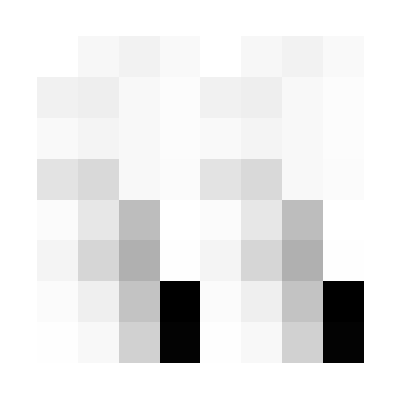
{-Graphics-,(-0.0053109 | -0.138633 | -0.227877 | -0.103876 | -0.0053109 | -0.138633 | -0.227877 | -0.103876
-0.247679 | -0.290428 | -0.112811 | -0.0503944 | 0.247679 | 0.290428 | 0.112811 | 0.0503944
0.108453 | -0.18563 | -0.114518 | -0.0553259 | 0.108453 | -0.18563 | -0.114518 | -0.0553259
-0.480872 | 0.64799 | 0.112376 | 0.07753 | 0.480872 | -0.64799 | -0.112376 | -0.07753
-0.0670001 | 0.421322 | -1.13493 | 0.00410123 | -0.0670001 | 0.421322 | -1.13493 | 0.00410123
0.195647 | -0.715908 | 1.35432 | 0.0142581 | -0.195647 | 0.715908 | -1.35432 | -0.0142581
0.0648705 | -0.272204 | 1.03771 | -4.39883 | -0.0648705 | 0.272204 | -1.03771 | 4.39883
-0.0163136 | 0.129456 | -0.793669 | 4.35218 | -0.0163136 | 0.129456 | -0.793669 | 4.35218)}

```mathematica
(* Doing the first eigensystem calculation as a testing ground *)
{evals,evecs}=Eigensystem[{F,S}];(* Calculate the eigenvalues and eigenvectors *)
{evals,evecs}={evals[[#]],evecs[[#]]}&@Ordering[evals]; (* Sort them in ascending order *)
evecs=matNorm[#,S]&/@evecs; (* Normalize them w.r.t. the overlap matrix S *)
If[AllTrue[Thread[#.S.#!=1]&/@evecs,TrueQ],Abort[],Nothing];(* Perform a numerical divergence check *)
#[evecs]&/@{ArrayPlot,MatrixForm}
```

```mathematica
ϵ=10^-6//N; (* Accuracy level *)
```

```mathematica
(* Reset before the while-loop to assert correctness *)
evals=ConstantArray[0.,{8}];
newEvals=evals+ϵ;
```

```mathematica
normDiffList={}; (* List of the norm of the differences *)
```

```mathematica
(* While the new and previous eigenvalues are still different enough... *)
While[Norm[newEvals-evals]>ϵ,
AppendTo[normDiffList,Norm[newEvals-evals]]; (* Append the norm of the difference to the normDiffList list *)
newEvals=evals;(* Overwrite the previous eigenvalues *)
G=Array[∑_(r=1)^8 ∑_(s=1)^8 Subscript[P, r,s](2 Subscript[Q, #1,r,#2,s]-Subscript[Q, #1,r,s,#2])&,{8,8}] (* Subscript[G, p,q] matrix *);
F=H+1/2 G;(* Compute the Fock operator from the G matrix *)
{evals,evecs}=Eigensystem[{F,S}];(* Calculate the eigenvalues and eigenvectors *)
{evals,evecs}={evals[[#]],evecs[[#]]}&@Ordering[evals]; (* Sort them in ascending order *)
evecs=matNorm[#,S]&/@evecs; (* Normalize them w.r.t. the overlap matrix S *)
If[AllTrue[Thread[#.S.#!=1]&/@evecs,TrueQ],Abort[],Nothing];(* Perform a numerical divergence check *)
(* Calculate the density matrix from the eigenvector Subscript[evecs, 1] associated with the minimal eigenvalue *)
P=2TensorProduct[Subscript[evecs, 1],Subscript[evecs, 1]];
]//AbsoluteTiming//First
```

0.05739

```mathematica
(* Return the first eigenvalue and the equilibrium bonding energy, where 1/d is the Subscript[E, nucl] term *)
Quantity[#,"HartreeEnergy"]&/@{Subscript[evals, 1],Total[P(H+1/4 G),2]+1/d}
UnitConvert[#, "Electronvolts"]&/@%
```

{-0.669956 E_h,-1.07855 E_h}

{-18.2304 eV,-29.3488 eV}

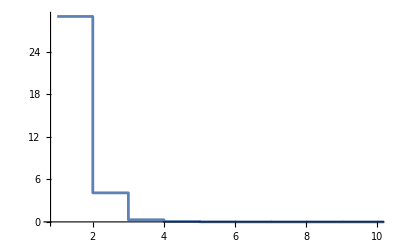

```mathematica
ListStepPlot[Drop[normDiffList,1],PlotRange->Full] (* Measurements give 0.05 seconds for the convergence time for an SCF loop *)
```